```mathematica
Eff=Import[NotebookDirectory[]<>"../calc/efficencies.txt","Table"];
Eff//MatrixForm
EffErr=Import[NotebookDirectory[]<>"../calc/efficencies_error.txt","Table"];
EffErr//MatrixForm
```

(0.980811 | 0.000011 | 0.010061 | 0.000122
0.00016 | 0.890762 | 0.003585 | 0.
0.01259 | 0.031002 | 0.848524 | 0.000457
0. | 0. | 0.001868 | 0.966965)

(0.000448 | 0.000011 | 0.000355 | 0.000035
0.000041 | 0.001015 | 0.000212 | 0.
0.000364 | 0.000564 | 0.001274 | 0.000068
0. | 0. | 0.000153 | 0.000569)

{0.464439,-0.710019,-0.917529,-0.346142,-0.323092}

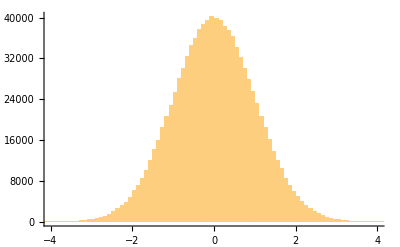

```mathematica
rns=RandomVariate[NormalDistribution[],1000000];
rns[[1;;5]]
Histogram[rns,100,PlotRange->{{-4,4},All}]
```

```mathematica
NoisyInvEff=Inverse[Eff+EffErr*#]&/@rns;
```

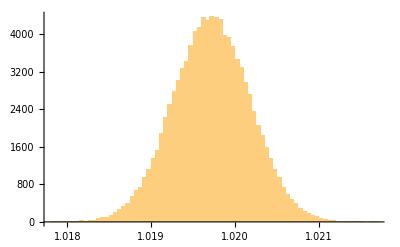

```mathematica
Histogram[NoisyInvEff[[All,1,1]],100,PlotRange->{All,All}]
```

```mathematica
NoisyInvEffSort=Table[NoisyInvEff[[All,i,j]],{i,1,4},{j,1,4}];
Inverse[Eff]
A=Mean[#]&/@#&/@NoisyInvEffSort;
A//MatrixForm
EffErr//MatrixForm
sA=StandardDeviation[#]&/@#&/@NoisyInvEffSort;
sA//MatrixForm
```

{{1.01972,0.000408268,-0.0120923,-0.000122941},{-0.000122288,1.1228,-0.00474236,2.25673×10^-6},{-0.0151257,-0.0410291,1.17887,-0.000555241},{0.00002922,0.0000792608,-0.00227736,1.03416}}

(1.01972 | 0.000408505 | -0.0120922 | -0.000122932
-0.000122192 | 1.1228 | -0.00474206 | 2.27714×10^-6
-0.0151255 | -0.0410284 | 1.17887 | -0.000555185
0.0000292858 | 0.000079366 | -0.00227727 | 1.03416)

(0.000448 | 0.000011 | 0.000355 | 0.000035
0.000041 | 0.001015 | 0.000212 | 0.
0.000364 | 0.000564 | 0.001274 | 0.000068
0. | 0. | 0.000153 | 0.000569)

(0.000456109 | 8.64048×10^-6 | 0.000403077 | 0.0000357369
0.0000414769 | 0.00126703 | 0.000267497 | 4.69164×10^-7
0.000406348 | 0.00063869 | 0.00174553 | 0.0000811472
3.16263×10^-6 | 7.6805×10^-6 | 0.000181808 | 0.000608273)

```mathematica
Threshold[Eff.A,10^-6]//MatrixForm
```

(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 0.999999)

```mathematica
Export[NotebookDirectory[]<>"../calc/invEfficencies_Math.txt",A,"Table"];
Export[NotebookDirectory[]<>"../calc/invEfficencies_error_Math.txt",sA,"Table"];
```